# Modèle mathématique: Oral B Pro 690

## Le Fay Yvann

### Intensité d’alimentation du moteur .

On associe l’intensité de l’alimentation du moteur à une transformation affine de la fonction de Clausen d’ordre 2.

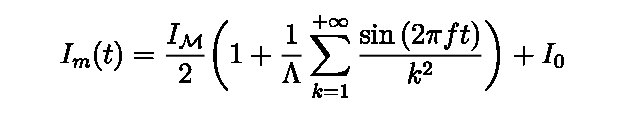

```mathematica
<<MaTeX`
MaTeX["I_m(t)=\\frac{I_{\\mathcal{M}}}{2}\\bigg( 1+\\frac{1}{\\Lambda} \\sum_{k=1}^{+\\infty}{\\frac{\\sin{(2\\pi f t)}}{k^2}}\\bigg)+I_0",Magnification->3]
```

```mathematica
Cl2[θ_]:=Sum[Sin[k θ]/k^2,{k,1,100}]; λ = MaxValue[Cl2[θ],{θ}];
INT[t_]:= IM/2(1+Cl2[2π f t]/λ)+I0;
```

```mathematica
T= Import["/home/hallelujah/Desktop/MESURES_E.ods",{"Data",1}];
```

```mathematica
f=DeleteCases[Abs[Fourier[T[[All,2]]]],x_/;x<100][[1]]
avI = Mean[T[[All,2]]];mI = Max[T[[All,2]]];I0=2avI-mI;IM=mI-I0;
ψ=(t/.FindMaximum[INT[t],{t,0,1/f}][[2]])-Part[T,Position[T,mI][[1,1]]][[1]];
```

900.743

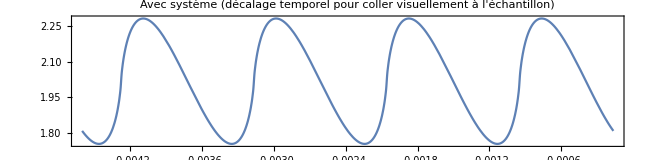

```mathematica
GraphicsRow[{ListLinePlot[T,ImageSize->{650,160}, Frame->True,AspectRatio->Full,FrameLabel->MaTeX/@{"t","I_m(t)"},PlotLabel->"Mesure avec système"],Plot[{INT[t+ψ]+0.1},{t,ψ+0,4/f+ψ},PlotLabel->"Avec système (décalage temporel pour coller visuellement à l'échantillon)",AspectRatio->Full,Frame->True,ImageSize->{650,160},FrameLabel->MaTeX/@{"t","I_m(t)"}]}]
```

### Force électromotrice et vitesse de rotation .

En régime transitoire

```mathematica
MaTeX["E_{\\approx}(t)=U_m+\\frac{L I_{\\mathcal{M}}}{2\\Lambda}\\ln|2\\sin{(\\pi f t)}|-rI_m(t)",Magnification->3]
```

-Graphics-

```mathematica
avω=1130;L=1.02*10^(-3); r = 0.255;Um=1.2; Ke=1/avω (Um-r(IM/2+I0));
EM[t_]:=Um+L IM/(2λ) Log[Abs[2Sin[π f t]]]-r INT[t];
Ke2=f/avω NIntegrate[EM[t],{t,0,1/f}]
```

0.000587927

```mathematica
Ke3=0.0005879270256552248;
ω[t_]:=EM[t]/Ke2;
```

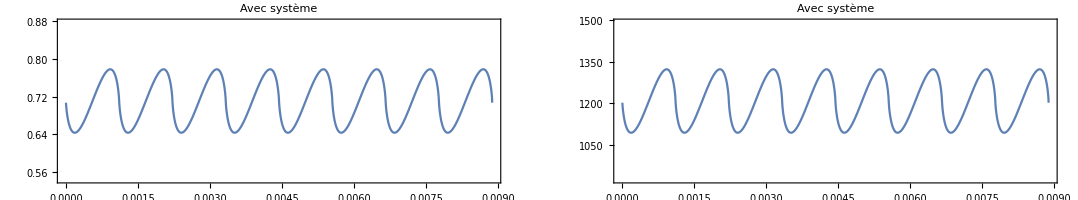

```mathematica
GraphicsRow[{Plot[EM[t],{t,0,8/f},PlotRange->{Um-r(IM+I0)-.1,Um-r I0+.1},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","E_\\approx(t)"}],Plot[ω[t],{t,0,8/f},PlotRange->{1/Ke2(Um-r(IM+I0)-.1),1/Ke2(Um-r I0+.1)},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","\\omega(t)"}]}]
```

### Couple moteur et différence entre couple moteur et couple résistant .

```mathematica
MaTeX["C_m(t)=K_i I_m(t) \\indent C_m(t)-C_r(t)=J\\frac{\\mathrm{d}\\omega}{\\mathrm{d}t}",Magnification->3]
```

-Graphics-

```mathematica
Lp=15*10^(-3); θ=π/2; R2=13*10^(-3)/2; r1=10*10^(-3)/2; ρp=7850; a=4*10^(-3); b=2.5*10^(-3); ra=2*10^(-3)/2; La=41*10^(-3); ρa=8900; ρc=8920; K=4*10^(-3); fF=19*10^(-3); fp=16*10^(-3); dp = 3*10^(-3); d=7*10^(-3); Rc1=4*10^(-3)/2; Rr=5.4/2*10^(-3); ρrr=8800; Lrr=5*10^(-3); J=3ρp Lp( θ /4(R2^4-r1^4)+a b (a^2+b^2)/12)+Pi/2 ra^4 ρa La+3ρc (Integrate[(x^2+y^2),{x,0,d},{y,0,K},{z,0,fF}]-Integrate[(x^2+y^2),{x,0,dp},{y,0,K},{z,0,fp}])+Pi/2ρp Lp (Rc1^4-ra^4)+Pi/2 ρrr Lrr (Rr^4-ra^4); J2=π/2R2^4*ρc*La ;
```

```mathematica
Ki=(5.06-3.37)/(2.943-1.962)*1/10^(3);
```

```mathematica
CM[t_]:=Ki INT[t];
DCmr[t_]:=J D[EM[t]];DCmr2[t_]:=J2 D[EM[t]];
En[t_]:=1/2J ω[t]^2;En2[t_]:=1/2 J2 ω[t]^2;
```

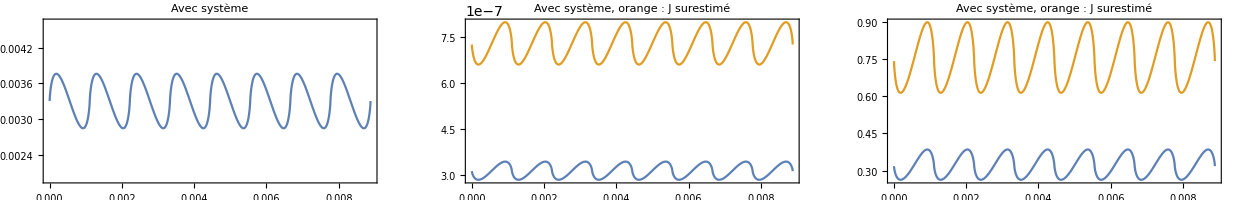

```mathematica
GraphicsRow[{Plot[CM[t],{t,0,8/f},PlotRange->{Ki (I0-.5),Ki(I0+IM+.5)},PlotLabel->"Avec système", ImageSize->{380,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","C_m(t)"}],Plot[{DCmr[t], DCmr2[t]},{t,0,8/f},PlotLabel->"Avec système, orange : J surestimé", ImageSize->{380,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","C_m(t)-C_r(t)"}], Plot[{En[t], En2[t]},{t,0,8/f},PlotLabel->"Avec système, orange : J surestimé", ImageSize->{380,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","\\frac{1}{2}J \\omega^2(t)"}]}]
```

### Autonomie de la brosse à dent .

```mathematica
MaTeX["\\mathcal{A}\\approx \\frac{\\mathcal{C}_T}{f \\int_{0}^{\\frac{1}{f}}{I_m(t)\\mathrm{d}t}}",Magnification->3]
```

-Graphics-

```mathematica
Ct=1.050; 
Ct/(f NIntegrate[INT[t],{t,0,1/f}])*60
```

32.8347

### Position en sortie de moteur .

```mathematica
MaTeX["\\theta_m(t)=\\frac{1}{K_e}\\int{E_{\\approx\\, L\\to 0}(t)}",Magnification->3]
MaTeX["\\theta_m(t)=\\frac{t}{K_e}\\bigg(U_m-r\\bigg(\\frac{I_\\mathcal{M}}{2}+I_0\\bigg)\\bigg)",Magnification->3]
```

-Graphics-

-Graphics-

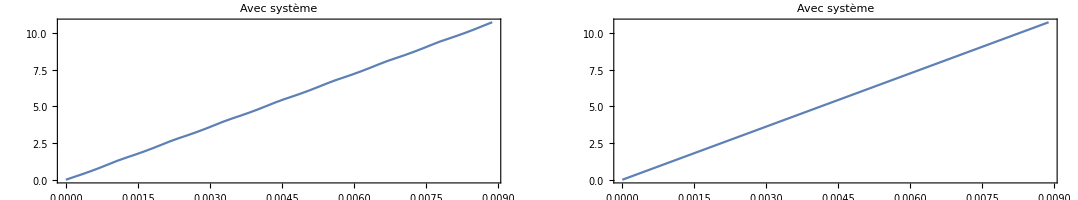

```mathematica
θm[t_]:=1/(Ke3) (t Um-r t (IM/2+I0)+r IM/(4π f λ)(-Zeta[3]+Sum[Cos[2π f k t]/k^3,{k,1,100}]));
θm2[t_]:=t/(Ke3)(Um-r(IM/2+I0));
GraphicsRow[{Plot[θm[t],{t,0,8/f},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","\\theta_m(t)"}],Plot[θm2[t],{t,0,8/f},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","\\approx \\theta_m(t)"}]}]
```

### Sortie du système bielle-manivelle .

En considérant une liste de couple valeur d'entrée / valeur de sortie, obtenue par simulation du système sur Fusion 360.

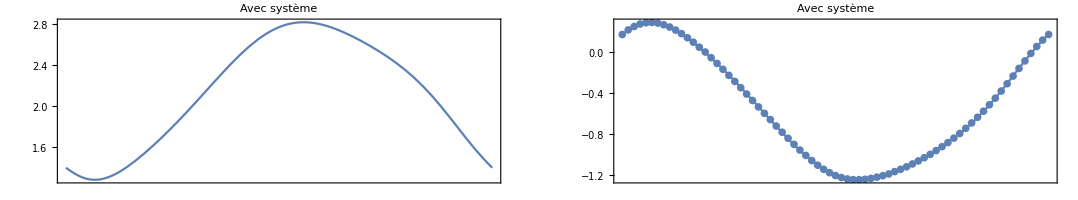

```mathematica
𝒟=Import["/home/hallelujah/Desktop/ok.ods",{"Data",1}];
F=Fit[𝒟,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
θS[x_]=Pi/2-F;
GraphicsRow[{Plot[θS[x],{x,0,2π},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None},{Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,Pi/4 Range[0,8]}],None}},FrameLabel->MaTeX/@{"\\theta","\\theta_S(\\theta)"}],Show[Plot[F,{x,0,2π}], ListPlot[𝒟],PlotLabel->"Avec système", ImageSize->{500,180}, AspectRatio->Full, Frame->True, FrameStyle->BlackFrame, FrameTicks->{{Automatic,None},{Table[{x, MaTeX[x, "DisplayStyle"->False]},{x,Pi/4 Range[0,8]}],None}},FrameLabel->MaTeX/@{"\\theta","\\frac{\\pi}{2}-\\theta_S[\\theta]"}]}]
```

### Sortie du système bielle-manivelle .

```mathematica
MaTeX["\\theta_S(t)=\\theta_S(R\\theta_m(t)[2\\pi])",Magnification->3]
```

-Graphics-

8632.56

True

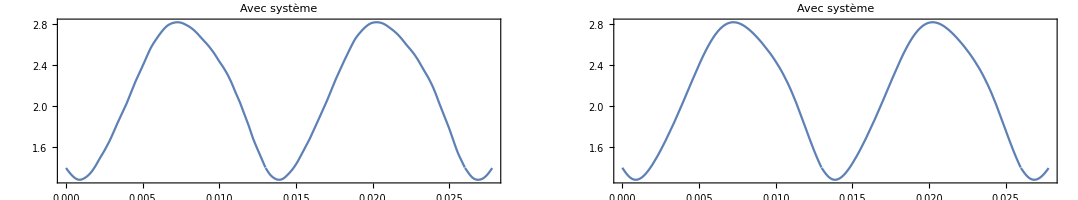

```mathematica
R=0.4; fBM = R/(2π Ke) (Um-r(IM/2+I0));
θST[t_]:=θS[Mod[R θm[t],2π]]; θST2[t_]:=θS[Mod[R θm2[t],2π]];
2*60*fBM
60/Pi*avω*R==2*60*fBM
GraphicsRow[{Plot[θST[t],{t,0,2/fBM},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","\\theta_S(t)"}],Plot[θST2[t],{t,0,2/fBM},PlotLabel->"Avec système", ImageSize->{500,180},AspectRatio->Full,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None}},FrameLabel->MaTeX/@{"t","\\approx\\theta_S(t)"}]}]
```